```mathematica
Hmb[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ11=Δ0,Δ12=0,H11,H12,H22,ϵ=0},H11=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H22=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(ϵ-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H12=KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ12*IdentityMatrix[dim,SparseArray]]];Chop@ArrayFlatten[{{H11,H12},{H12,H22}}]]
```

```mathematica
Hmb[1,.2,.2,.1,5,4]//MatrixForm
```

(49.9 | -25. | 0 | 0 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-25. | 49.9 | -25. | 0 | 2.5 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -25. | 49.9 | -25. | 0 | 2.5 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -25. | 49.9 | 0 | 0 | 2.5 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0
0 | 2.5 | 0 | 0 | 49.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0
-2.5 | 0 | 2.5 | 0 | -25. | 49.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0
0 | -2.5 | 0 | 2.5 | 0 | -25. | 49.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0
0 | 0 | -2.5 | 0 | 0 | 0 | -25. | 49.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2
0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -49.7 | 25. | 0 | 0 | 0 | 2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -49.7 | 25. | 0 | -2.5 | 0 | 2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -49.7 | 25. | 0 | -2.5 | 0 | 2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -49.7 | 0 | 0 | -2.5 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | -2.5 | 0 | 0 | -49.9 | 25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | -2.5 | 0 | 25. | -49.9 | 25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | -2.5 | 0 | 25. | -49.9 | 25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | 0 | 0 | 25. | -49.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 50.9 | -25. | 0 | 0 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | -25. | 50.9 | -25. | 0 | 2.5 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | -25. | 50.9 | -25. | 0 | 2.5 | 0 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | -25. | 50.9 | 0 | 0 | 2.5 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 2.5 | 0 | 0 | 50.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | -2.5 | 0 | 2.5 | 0 | -25. | 50.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | -2.5 | 0 | 2.5 | 0 | -25. | 50.7 | -25. | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | -2.5 | 0 | 0 | 0 | -25. | 50.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2
0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -50.7 | 25. | 0 | 0 | 0 | 2.5 | 0 | 0
0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -50.7 | 25. | 0 | -2.5 | 0 | 2.5 | 0
0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -50.7 | 25. | 0 | -2.5 | 0 | 2.5
0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 25. | -50.7 | 0 | 0 | -2.5 | 0
0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | -2.5 | 0 | 0 | -50.9 | 25. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | -2.5 | 0 | 25. | -50.9 | 25. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | -2.5 | 0 | 25. | -50.9 | 25.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 0 | 0 | 0 | 25. | -50.9)

```mathematica
data=Block[{vzm=1,vzstep=0.01,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[SparseArray@Hmb[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2126,19].

Kernels::rdead: Subkernel connected through KernelObject[8,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {49} assigned to KernelObject[8,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2125,18].

Kernels::rdead: Subkernel connected through KernelObject[7,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {50} assigned to KernelObject[7,local,<defunct>].

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.2\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2124,17].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[6,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {51} assigned to KernelObject[6,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[8,local,<defunct>] resurrected as KernelObject[9,local].

LaunchKernels::clone: Kernel KernelObject[7,local,<defunct>] resurrected as KernelObject[10,local].

LaunchKernels::clone: Kernel KernelObject[6,local,<defunct>] resurrected as KernelObject[11,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

```mathematica
data2=Block[{vzm=1,vzstep=0.01,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

```mathematica
Dynamic[vz]
```

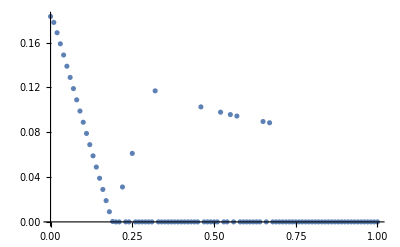

```mathematica
ListPlot[data,DataRange->{0,1}]
```